```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`
<<ISTPackage`LS`;
```

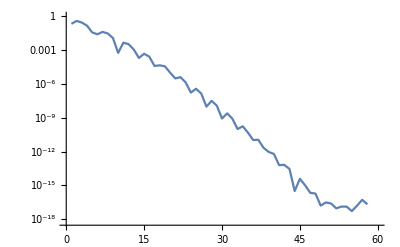
{1.92875×10^-22,-Graphics-}

```mathematica
Fhathat//Clear;Fhat//Clear;
F[x_]:=Exp[-x^2/2]/.Indeterminate->0./.Underflow[]->0.;
FF=FT[F,60,10];
Fhat[k_]:=Fhat[k]=FF[k];
Fhat[_?InfinityQ]:=0.;
```

```mathematica
Fhat[1000]
```

1.74725×10^-16-2.71918×10^-16 ⅈ

```mathematica
Fhat[3+I]
g[3+I]//N
```

-0.045451-0.00647889 ⅈ

-0.045451-0.00647889 ⅈ

```mathematica
g[X_]:=Sqrt[2Pi]Exp[-X^2/2];
```

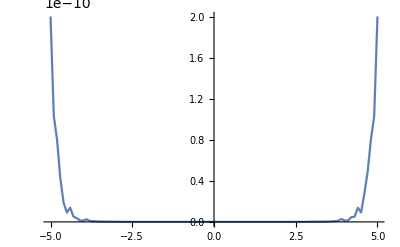

```mathematica
TablePlot[(Fhat[X]-g[X])/g[X]//Abs,{X,-5,5,.1},PlotRange->All]
```

```mathematica
LSSetnu[1];
qLS//Clear;
qLS[x_,t_]:=qLS[x,t]=LS[Fhat,x,t]
```

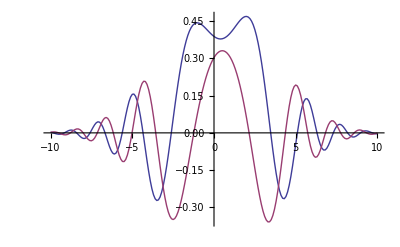

```mathematica
Monitor[ReImTablePlot[qLS[x,1],{x,-10,10,.1},PlotRange->All],x]
```